```mathematica
(* rozwiązywanie równań *)
```

1.  Rozwiąż równanie.

```mathematica
Solve[x^2-2x+5==0,x]
```

{{x→1-2 ⅈ},{x→1+2 ⅈ}}

Rozwiązywanie systemu równań

```mathematica
Solve[{0.1 x+2.3 y==13.7,-3.4 x+6.1 y==3.5},{x,y}]
```

{{x→8.95848,y→5.56702}}

Rozwiązywanie równania z zakresem

```mathematica
Solve[{Cos[2*x^2]==1,Element[x,Reals],0≤ x≤Pi},x]
```

{{x→0},{x→0},{x→0},{x→0},{x→√π},{x→√π},{x→√(2 π)},{x→√(2 π)},{x→√(3 π)},{x→√(3 π)}}

Równania różniczkowe

```mathematica
DSolve[(1-3/y[x]+x)y'[x]+y[x]==3/x-1,y[x],x]
```

Solve[(2^(2/3) (1-((-3+x+x^2) (6+(1+x) y[x]))/((1+x) (((-3+x+x^2)^3)/(1+x)^3)^(1/3) (-3+(1+x) y[x]))) (2+((-3+x+x^2) (6+(1+x) y[x]))/((1+x) (((-3+x+x^2)^3)/(1+x)^3)^(1/3) (-3+(1+x) y[x]))) (-3+Log[2^(2/3) (1-((-3+x+x^2) (6+(1+x) y[x]))/((1+x) (((-3+x+x^2)^3)/(1+x)^3)^(1/3) (-3+(1+x) y[x])))] (1-((-3+x+x^2) (6+(1+x) y[x]))/((1+x) (((-3+x+x^2)^3)/(1+x)^3)^(1/3) (-3+(1+x) y[x])))+Log[2^(2/3) (2+((-3+x+x^2) (6+(1+x) y[x]))/((1+x) (((-3+x+x^2)^3)/(1+x)^3)^(1/3) (-3+(1+x) y[x])))] (-1+((-3+x+x^2) (6+(1+x) y[x]))/((1+x) (((-3+x+x^2)^3)/(1+x)^3)^(1/3) (-3+(1+x) y[x])))))/(9 (-2+(3 (-3+x+x^2) (6+(1+x) y[x]))/((1+x) (((-3+x+x^2)^3)/(1+x)^3)^(1/3) (-3+(1+x) y[x]))-(6+(1+x) y[x])^3/(-3+(1+x) y[x])^3))==C[1]+(2^(2/3) (-3+x+x^2) (x-3 Log[x]+3 Log[1+x]))/(27 (1+x) (((-3+x+x^2)^3)/(1+x)^3)^(1/3)),y[x]]

```mathematica
DSolve[{x+y[x]*Exp[y[x]/x]==x Exp[y[x]/x]*y'[x], y[1]==0},y[x],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{y[x]→x Log[1+Log[x]]}}

2. Równanie różniczkowe z warunkiem początkowym i znalezienie wartości funkcji f dla x=7/2.

```mathematica
sol=DSolve[{y'[x]==y[x]x,y[1]==2},y[x],x]
f[x_]:=Evaluate[y[x]/.sol[[1]]]
f[7/2]
```

{{y[x]→2 ⅇ^(-1/2+x^2/2)}}

2 ⅇ^(45/8)

LISTY I OPERACJE
1. Wybierz losowo liczbę całkowitą z przedziału <0, 20>  i sprawdź, czy wybrana liczba jest liczbą
pierwszą. Wybierz losowo liczbę rzeczywistą z przedziału <100, 100> i sprawdź, czy wybrana
liczba jest całkowita. Przydatne funkcje: RandomReal, RandomInteger, PrimeQ, IntegerQ,itp.

```mathematica
randomInteger=RandomInteger[{0,20}];
If[PrimeQ[randomInteger],
    Print[randomInteger," jest liczba pierwszą."],
   Print[randomInteger," nie jest liczba pierwszą."]]
```

10 nie jest liczba pierwszą.

```mathematica
randomReal=RandomReal[{-100,100}];
If[IntegerQ[randomReal],
Print[randomReal," jest liczba całkowitą."],
Print[randomReal," nie jest liczba całkowitą."]]
```

-48.9827 nie jest liczba całkowitą.

2.  Utwórz listę kwadratów kolejnych liczb parzystych z przedziału <1, 10>. Rozszerz tę listę o
sześciany liczb nieparzystych z tego przedziału. Użyj obu utworzonych list, aby sprawdzić
działanie funkcji: Take, Drop, Delete, Insert, Join, Length, Position.

```mathematica
lista = Table[i^2, {i, 2, 10, 2}];
```

```mathematica
polaczonaLista=Join[lista,Table[i^3,{i,1,9,2}]];
polaczonaLista
```

{4,16,36,64,100,1,27,125,343,729}

Take - pobiera x pierwszych elementów z listy

```mathematica
Take[polaczonaLista,3]
```

{4,16,36}

Drop - usuwa pierwsze x elementów z listy

```mathematica
Drop[polaczonaLista,2]
```

{36,64,100,1,27,125,343,729}

Delete - usuwa element o danym indexie

```mathematica
Delete[polaczonaLista,4]
```

{4,16,36,100,1,27,125,343,729}

```mathematica
Length[polaczonaLista]
```

10

Position - index, gdzie znajduje się dana pozycja, np. liczba nr 16

```mathematica
Position[lista,16]
```

{{2}}

3. Utwórz tablicę dodatnich wielokrotności liczby 6 mniejszych od 100. Utwórz analogiczną tablicę
wielokrotności 8. Połącz obie listy, tak aby elementy powtarzające się występowały tylko raz.
Posortuj listę malejąco.

```mathematica
wielokrotnosc6=Table[i, {i,6,100,6}]
```

{6,12,18,24,30,36,42,48,54,60,66,72,78,84,90,96}

```mathematica
wielokrotnosc8=Table[i,{i,8,100,8}]
```

{8,16,24,32,40,48,56,64,72,80,88,96}

```mathematica
polaczoneWielokrotnosci=Union[wielokrotnosc6,wielokrotnosc8]
```

{6,8,12,16,18,24,30,32,36,40,42,48,54,56,60,64,66,72,78,80,84,88,90,96}

```mathematica
Sort[polaczoneWielokrotnosci,Greater]
```

{96,90,88,84,80,78,72,66,64,60,56,54,48,42,40,36,32,30,24,18,16,12,8,6}

4. Korzystając z podanej poniżej definicji, stwórz listę zawierającą 15 pierwszych elementów ciągu
Fibonacciego.

```mathematica
fibonacci[0]:=0
fibonacci[1]:=1
fibonacci[n_]:=fibonacci[n-1]+fibonacci[n-2]

fibonacciList=Table[fibonacci[n],{n,0,14}]
```

{0,1,1,2,3,5,8,13,21,34,55,89,144,233,377}

5. Utwórz 15-elementową listę l1 losowo wygenerowanych liczb rzeczywistych z przedziału (−1, 1).
Utwórz listę l2 zawierającą tylko ujemne elementy listy l1. Policz ile jest elementów ujemnych, a ile dodatnich w l1. Zsumuj elementy listy l1. Przydatne funkcje: Total, Count[lista, _?Positive] itp.

```mathematica
l1=Table[RandomReal[{-1,1}],{i,1,15}]
```

{0.728743,-0.844021,-0.614287,0.247634,0.695043,0.63311,-0.0846246,-0.0715381,0.295772,-0.862815,0.261518,-0.838626,-0.700637,0.0359393,0.513252}

```mathematica
l2=Select[l1,#<0&]
```

{-0.844021,-0.614287,-0.0846246,-0.0715381,-0.862815,-0.838626,-0.700637}

```mathematica
Count[l1,_?Positive]
```

8

```mathematica
Count[l1,_?Negative]
```

7

```mathematica
Total[l1]
```

-0.605537

6.   Wygeneruj 10 losowych punktów płaszczyzny z kwadratu <-1, 1>x<−1, 1>,  a następnie wyznacz
dla tych punktów wartości funkcji f(x, y) = x^2 + y^2. Uszereguj utworzoną tablicę rosnąco
względem wartości funkcji celu f. Wypisz współrzędne punktów dla których wartość funkcji
jest najmniejsza i największa.

```mathematica
punkty=RandomReal[{-1,1},{10,2}]
```

{{0.826172,0.161056},{0.640748,0.48758},{0.410275,0.710128},{-0.884522,-0.277699},{-0.552847,0.9361},{-0.103758,0.00556801},{-0.411592,0.0364628},{0.388108,0.915068},{0.398527,-0.742367},{0.81091,0.711681}}

```mathematica
f[x_,y_]:=x^2+y^2
wyniki=Table[f[punkty[[i,1]],punkty[[i,2]]],{i,1,Length[punkty]}]
```

{0.708499,0.648293,0.672607,0.859496,1.18192,0.0107968,0.170738,0.987978,0.709933,1.16406}

```mathematica
posortowane=SortBy[punkty,f[#[[1]],#[[2]]]&]
```

{{-0.103758,0.00556801},{-0.411592,0.0364628},{0.640748,0.48758},{0.410275,0.710128},{0.826172,0.161056},{0.398527,-0.742367},{-0.884522,-0.277699},{0.388108,0.915068},{0.81091,0.711681},{-0.552847,0.9361}}

```mathematica
posortowane[[1]]
```

{-0.103758,0.00556801}

```mathematica
posortowane[[Length[posortowane]]]
```

{-0.552847,0.9361}

7.   Utwórz dowolne trzy macierze A, B oraz C i oblicz A + C, αB oraz AB. Zadbaj o prawidłowy rozmiar macierzy. Zbadaj różnicę pomiędzy działaniem A.B oraz AB. Utwórz macierz kwadratową i sprawdź działanie funkcji: Inverse, Det, Eigenvalues, IdentityMatrix, DiagonalMatrix etc.

```mathematica
(* tworzenie macierzy *)
```

```mathematica
A={{1,2,3},{2,3,5},{4,5,6}};
B={{0,1,1},{3,4,1},{6,8,1}};
CC={{9,8,7},{6,5,4},{3,2,1}};
```

```mathematica
A +CC
```

{{10,10,10},{8,8,9},{7,7,7}}

```mathematica
2*B
```

{{0,2,2},{6,8,2},{12,16,2}}

```mathematica
A*B
```

{{0,2,3},{6,12,5},{24,40,6}}

```mathematica
A.B
```

{{24,33,6},{39,54,10},{51,72,15}}

```mathematica
(* A*B mnoży wszystkie wartości przez siebie jakby macierz była skalarem, a A.B wykonuje mnożenie macierzy *)
```

```mathematica
K={{1,2},{3,4}};
Inverse[K]
```

{{-2,1},{3/2,-1/2}}

```mathematica
Det[K]
```

-2

```mathematica
Eigenvalues[K]
```

{1/2 (5+√33),1/2 (5-√33)}

```mathematica
IdentityMatrix[2]
```

{{1,0},{0,1}}

```mathematica
DiagonalMatrix[2,2]
```

DiagonalMatrix::vector: Argument 2 at position 1 is not a non-empty vector.

```mathematica
DiagonalMatrix[{2,2}]
```

{{2,0},{0,2}}

```mathematica
?DiagonalMatrix
```

```mathematica
Transpose[K]
```

{{1,3},{2,4}}

```mathematica
Diagonal[K]
```

{1,4}

```mathematica
Tr[K]
```

5

8.  Rozwiąż równanie macierzowe:

```mathematica
a1={{1,2},{-1,0}};
a2=Inverse[{{1,1},{2,3}}];
a3=Transpose[{{2,3},{1-i,i}}];
```

```mathematica
Solve[a1*X*a2== a3, X]
```

Solve::ivar: {0,14} is not a valid variable.

Solve[False,{{0,14},{3,45/2}}]

```mathematica
X=a3*Inverse[a2]*Inverse[a1]
```

{{0,14},{3,45/2}}

## Wykresy i animacje

1. Korzystając z instrukcji ListPlot, stwórz wykres (w układzie współrzędnych) 15 elementów ciągu an =(−1)^n/n+1 . Wyrównaj jednostki na osiach, oznacz oś OX jako „n”, zaś oś OY jako „a[n] ”, pokoloruj tło kolorem jasnoszarym, zaznacz punkty reprezentujące elementy ciągu kolorem niebieskim, połącz punkty liniami. Korzystając z funkcji Interpolation znajdź funkcję interpolacyjną dla ciągu. Narysuj jej wykres. Umieść wykres ciągu i funkcji interpolującej na jednym wykresie. Sprawdź działanie AspectRatio.

```mathematica
f[n_]:=(-1)^n/(n+1);
ciag=Table[f[n],{n,1,15}]
```

{-1/2,1/3,-1/4,1/5,-1/6,1/7,-1/8,1/9,-1/10,1/11,-1/12,1/13,-1/14,1/15,-1/16}

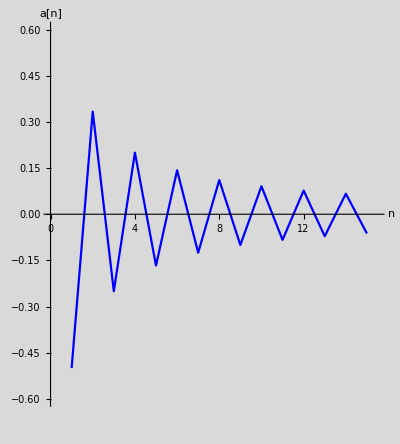

```mathematica
wykresCiagu=ListPlot[ciag,PlotRange->{{0,15.5},{-0.6,0.6}},AxesLabel->{"n","a[n]"},Background->LightGray, PlotStyle->Blue,Joined->True,AspectRatio->1/0.9]
```

```mathematica
(* wykres funkcji interpolacyjnej *)
```

```mathematica
inter=Interpolation[ciag]
```

InterpolatingFunction[…]

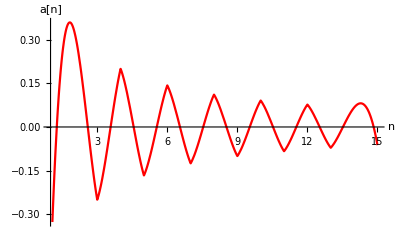

```mathematica
wykresInterpolacji=Plot[inter[x],{x,1,15},AxesLabel->{"n","a[n]"},PlotStyle->Red,AspectRatio->1/GoldenRatio]
```

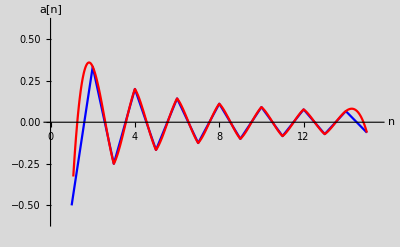

```mathematica
Show[wykresCiagu,wykresInterpolacji]
```

2. Wykorzystaj tablicę wartości ciągu z poprzedniego przykładu do sprawdzenia działania funkcji
Fit oraz FindFit.

```mathematica
Clear[x]
```

```mathematica
Fit[ciag,{1,x},x]
```

-0.0805939+0.00726483 x

```mathematica
Fit[ciag,{1,x,x^2},x]
```

-0.212619+0.0538621 x-0.00291233 x^2

```mathematica
FullSimplify[-0.21261938610839742+0.05386207188182796 x-0.002912327406307695 x^2]
```

-0.212619+(0.0538621-0.00291233 x) x

```mathematica
FindFit[ciag,a x,{a},x]
```

{a→-0.000534574}

3. Narysuj wykres funkcji f(x) = x^n for x ∈ {1, 2, 3} oraz x ∈ <0, 2>. Pokoloruj linie wykresu odpowiedni kolorem czerwonym, zielonym, niebieskim, a tło kolorem jasno szarym. Podpisz odpowiednio osie. Przedstaw wykresy w jednym układzie współrzędnych (instrukcja Show). Powtórz rysunek, ale zamiast pełnego tła wypełnij szarym kolorem odstępy między linią wykresu a osią OX (instrukcje Filling i FillingStyle ).